Autor: Dawid Bitner

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 7

Metoda różnic skończonych

Napisać procedurę realizującą metodę różnic skończonych dla zagadnienia brzegowego liniowego równania różniczkowego zwyczajnego rzędu drugiego. Działanie procedury przetestować na przykładzie podanym na wykładzie.

Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone zagadnienia brzegowego:

{m y''(x)+ k y'(x) +s y(x)=0,  x∈[0,10],
y(0)=1, y(10)=1,

Obliczenia wykonać dla dwóch zestawów danych:
a) m=1, k=3, s=2;
b) m=5, k=2, s=10.

Za każdym razem obliczenia wykonać dla 500 i 1000 kroków.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązania przybliżone.
Wykreślić także, na jednym rysunku, błędy uzyskanych rozwiązań przybliżonych.
Policzyć ponadto błędy maksymalne oraz średnie dla obu siatek oraz zestawić je na wykresie słupkowym, np. postaci:

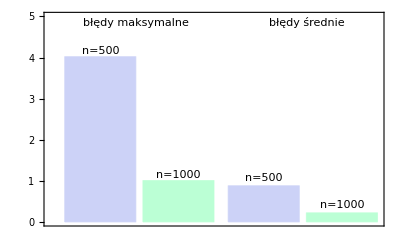

## Rozwiązanie

```mathematica
(* Metoda Różnic Skończonych *)
rs[m_,k_,s_,t_,a_,b_,α1_,α2_, β1_, β2_,za_,zb_,n_]:=Module[{
result,
h = (b-a)/n,
equations
},
X= Table[a+i*h,{i,0,n}];
Y=Array[y, n+1];
equations = Table[0, {i,0,n}];
equations⟦1⟧ = (2*h*α1-3*α2)*y[1]+4α2*y[2]-α2*y[3] == 2*h*za;
(*equations⟦n+1⟧ =β1*y[n+1]+β2/(2h)(y[n-1]-4y[n]+3y[n+1])==zb;*)
equations⟦n+1⟧ = β2 *y[n-1]−4* β2 *y[n]+(2 *h *β1+3*β2)*y[n+1] == 2 * h * zb;
Do[
equations⟦i⟧=(m * (y[i+1]-2*y[i]+y[i-1])/h^2+k * (y[i+1]-y[i-1])/(2*h)+s * y[i] == t)/.{x->X⟦i⟧};
,{i,2,n}];
result = Solve[equations];
Return[result];
];
```

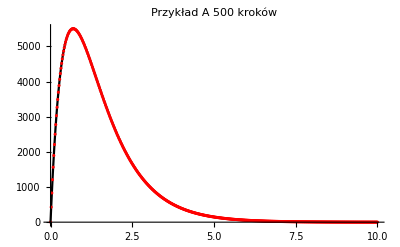

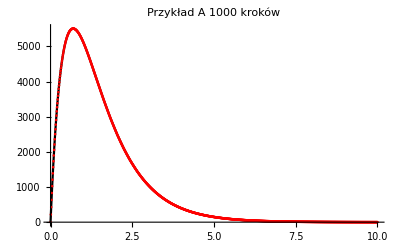

```mathematica
(* A *)
m = 1;
k = 3;
s = 2;
t =0;
a = 0;
b = 10;
α1 = 1;
α2 = 0;
β1 = 1;
β2 = 0;
za = 1;
zb = 1;
n = 500;
res = DSolve[{m*y''[x]+k*y'[x]+s*y[x]==0, y[0]==1, y[10]==1},y[x],x];
resA = res⟦1,1,2⟧;
resAPlot = Plot[resA,{x,0,10}, PlotStyle->{Black}, PlotRange->All];
res500A =rs[m,k,s,t,a,b,α1,α2,β1,β2,za,zb,500];
res1000A = rs[m,k,s,t,a,b,α1,α2,β1,β2,za,zb,1000];
res500ATab =Table[{(b-a)/500*(i-1), res500A⟦1,i,2⟧},{i,1,501}];
plot500A = ListPlot[res500ATab, PlotStyle->{Dashed, Red}, PlotRange->All];
res1000ATab =Table[{(b-a)/1000*(i-1), res1000A⟦1,i,2⟧},{i,1,1001}];
plot1000A = ListPlot[res1000ATab, PlotStyle->{Dashed, Red}, PlotRange->All];
Show[resAPlot, plot500A, PlotLabel->"Przykład A 500 kroków"]
Show[resAPlot, plot1000A, PlotLabel->"Przykład A 1000 kroków"]
resATab500 = Table[res⟦1,1,2⟧/.{x->xx},{xx, 0.,10,10/500}];
resATab1000 = Table[res⟦1,1,2⟧/.{x->xx},{xx, 0.,10,10/1000}];
```

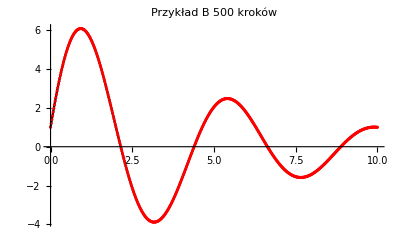

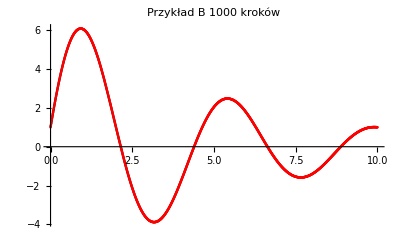

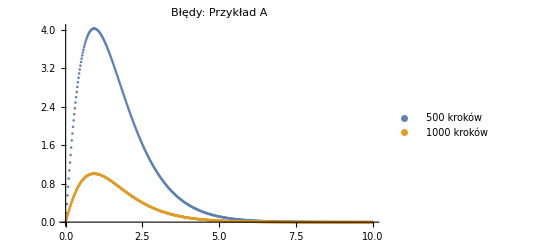

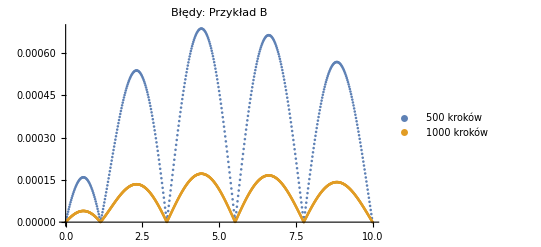

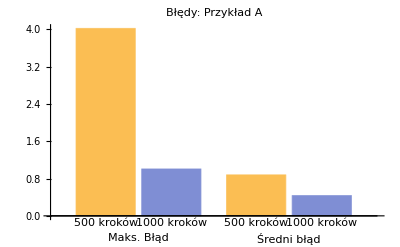

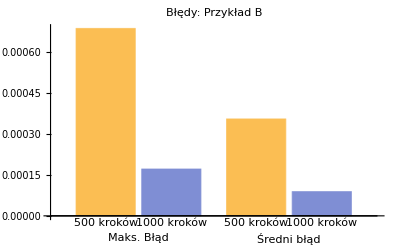

```mathematica
(* B *)
m=5;
k=2;
s=10;
res = DSolve[{m*y''[x]+k*y'[x]+s*y[x]==0, y[0]==1, y[10]==1},y[x],x];
resB = res⟦1,1,2⟧;
resBPlot = Plot[resB,{x,0,10}, PlotStyle->{Black}, PlotRange->All];
res500B =rs[m,k,s,t,a,b,α1,α2,β1,β2,za,zb,500];
res1000B = rs[m,k,s,t,a,b,α1,α2,β1,β2,za,zb,1000];
res500BTab =Table[{(b-a)/500*(i-1), res500B⟦1,i,2⟧},{i,1,501}];
plot500B = ListPlot[res500BTab, PlotStyle->{Dashed, Red}, PlotRange->All];
res1000BTab = Table[{(b-a)/1000*(i-1), res1000B⟦1,i,2⟧},{i,1,1001}];
plot1000B = ListPlot[res1000BTab, PlotStyle->{Dashed, Red}, PlotRange->All];
Show[resBPlot, plot500B, PlotLabel->"Przykład B 500 kroków"]
Show[resBPlot, plot1000B, PlotLabel->"Przykład B 1000 kroków"]

resBTab500 = Table[res⟦1,1,2⟧/.{x->xx},{xx, 0.,10,10/500}];
resBTab1000 = Table[res⟦1,1,2⟧/.{x->xx},{xx, 0.,10,10/1000}];

error500A   = Table[{ res500ATab⟦i,1⟧,   Abs[res500ATab⟦i,2⟧  -resATab500⟦i⟧]},{i,1,501}];
error1000A = Table[{ res1000ATab⟦i,1⟧, Abs[res1000ATab⟦i,2⟧-resATab1000⟦i⟧]},{i,1,1001}];
error500B   = Table[{ res500BTab⟦i,1⟧,   Abs[res500BTab⟦i,2⟧   -resBTab500⟦i⟧]},{i,1,501}];
error1000B = Table[ {res1000BTab⟦i,1⟧, Abs[res1000BTab⟦i,2⟧-resBTab1000⟦i⟧]},{i,1,1001}];
ListPlot[{error500A, error1000A},PlotLabel->"Błędy: Przykład A",PlotLegends->{LineLegend[{"500 kroków", "1000 kroków"}]}, PlotRange->All]
ListPlot[{error500B, error1000B},PlotLabel->"Błędy: Przykład B",PlotLegends->{LineLegend[{"500 kroków", "1000 kroków"}]}, PlotRange->All]

errors500A = Table[{error500A⟦i,2⟧}, {i, 1, Length[error500A]}];
maxError500A = Max[errors500A];
averageError500A = Mean[errors500A]⟦1⟧;

errors1000A = Table[{error1000A⟦i,2⟧}, {i, 1, Length[error500A]}];
maxError1000A = Max[errors1000A];
averageError1000A = Mean[errors1000A]⟦1⟧;

errors500B = Table[{error500B⟦i,2⟧}, {i, 1, Length[error500B]}];
maxError500B = Max[errors500B];
averageError500B = Mean[errors500B]⟦1⟧;

errors1000B = Table[{error1000B⟦i,2⟧}, {i, 1, Length[error1000B]}];
maxError1000B = Max[errors1000B];
averageError1000B = Mean[errors1000B]⟦1⟧;

barChartA = BarChart[{{maxError500A, maxError1000A}, {averageError500A, averageError1000A}}, ChartLabels->{{"Maks. Błąd", "Średni błąd"}, {"500 kroków", "1000 kroków"}}];
barChartB = BarChart[{{maxError500B, maxError1000B}, {averageError500B, averageError1000B}}, ChartLabels->{{"Maks. Błąd", "Średni błąd"}, {"500 kroków", "1000 kroków"}}];
Show[barChartA, PlotLabel->"Błędy: Przykład A"]
Show[barChartB, PlotLabel->"Błędy: Przykład B"]
```